```mathematica
BesselK[1,0.53]
```

1.53645

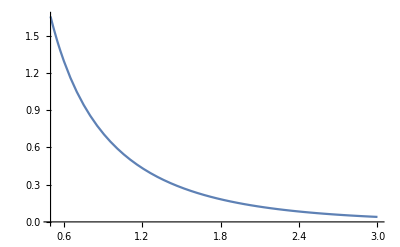

```mathematica
Plot[BesselK[1,x],{x,0.5,3}]
```

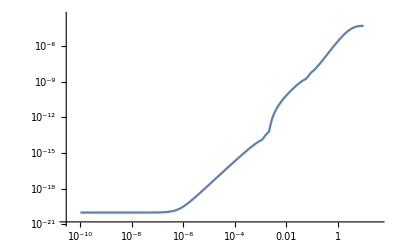

```mathematica
m=125;
g=100;
T=10^-15;
M=2.44 10^18;
p=3.14;

solution1=NDSolve[{y'[x]==((45*M*T)/(1.66* 4*p^4*m^2*g^(3/2)))*BesselK[1,x]*x^3,
y[10^-10]==10^-20},
y,{x,10^-10,10}];

LogLogPlot[Evaluate[y[x]/.solution1],{x,10^-10,10},PlotRange->{{0,100},{0,10^11}}];

Show[%]
```

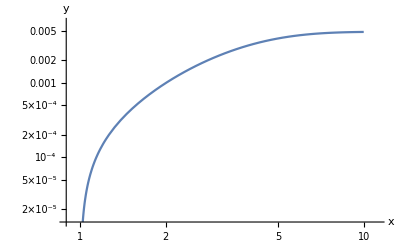

```mathematica
m=125;
g=100;
T=10^-13;
M=2.44 10^18;
p=3.14;

solution1=NDSolve[{y'[x]==((45*M*T)/(1.66* 4*p^4*m^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];

LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];

Show[%]
```

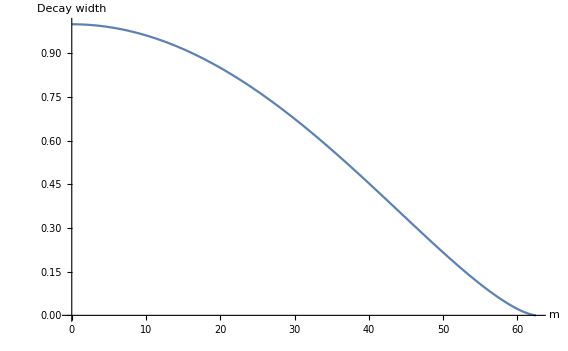

```mathematica
M=125;
Plot[y[m]=(1-4*m^2/M^2)^(3/2),{m,0,M/2},AxesLabel-> {Style[m,Medium,Black],Style["Decay width",Medium,Black]}]
```

```mathematica
m=10;
M=125;
h=10^-7;
T=(M*h^2/(8*3.14))(1-4*m^2/M^2)^(3/2)
```

4.80691×10^-14

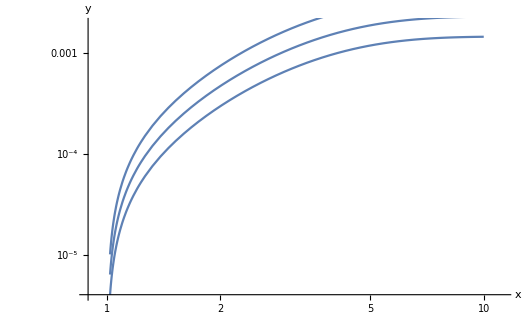

```mathematica
M=125;
m=10;
g=100;
h=10^-7;
h1=10^-6.9;
h11=10^-7.1;
T=(M*h^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
T1=(M*h1^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
T11=(M*h11^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
M0=2.44 10^18;
p=3.14;

solution1=NDSolve[{y'[x]==((45*M0*T)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];

solution11=NDSolve[{y'[x]==((45*M0*T1)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];
solution111=NDSolve[{y'[x]==((45*M0*T11)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];


LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];

LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution111],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];


Show[%,%%,%%%]
```

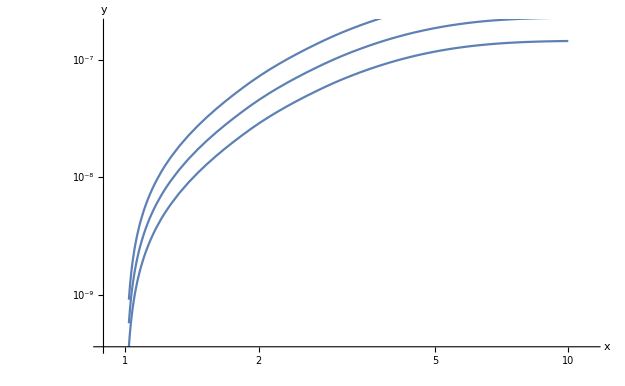

```mathematica
M=125;
m=10;
g=100;
h=10^-9;
h1=10^-8.9;
h11=10^-9.1;
T=(M*h^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
T1=(M*h1^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
T11=(M*h11^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
M0=2.44 10^18;
p=3.14;

solution1=NDSolve[{y'[x]==((45*M0*T)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];

solution11=NDSolve[{y'[x]==((45*M0*T1)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];
solution111=NDSolve[{y'[x]==((45*M0*T11)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];


LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];

LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution111],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];


Show[%,%%,%%%]
```

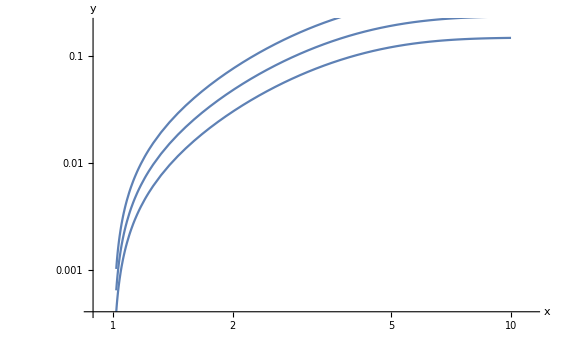

```mathematica
M=125;
m=10;
g=100;
h=10^-6;
h1=10^-5.9;
h11=10^-6.1;
T=(M*h^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
T1=(M*h1^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
T11=(M*h11^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
M0=2.44 10^18;
p=3.14;

solution1=NDSolve[{y'[x]==((45*M0*T)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];

solution11=NDSolve[{y'[x]==((45*M0*T1)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];
solution111=NDSolve[{y'[x]==((45*M0*T11)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];


LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];

LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution111],{x,1,10},PlotRange->{{0,100},{0,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];


Show[%,%%,%%%]
```

```mathematica
PlotLegends->{"h=10^-8.9"},PlotStyle->{Red},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium], PlotLegends->{"ν_e→ν_e"},ImageSize->Large];
```

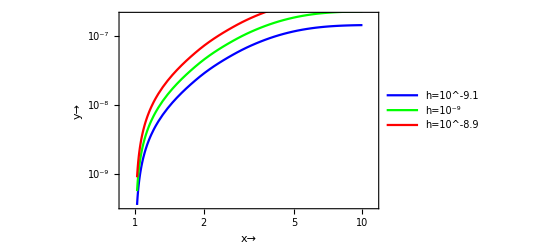

```mathematica
M=125;
m=10;
g=100;
h=10^-8.9;
h1=10^-9;
h11=10^-9.1;
T=(M*h^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
T1=(M*h1^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
T11=(M*h11^2/(8*3.14))(1-4*m^2/M^2)^(3/2);
M0=2.44 10^18;
p=3.14;

solution1=NDSolve[{y'[x]==((45*M0*T)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];

solution11=NDSolve[{y'[x]==((45*M0*T1)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];
solution111=NDSolve[{y'[x]==((45*M0*T11)/(1.66* 4*p^4*M^2*g^(3/2)))*BesselK[1,x]*x^3,
y[1]==10^-20},
y,{x,1,10}];


LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{0,100},{0,10^11}},PlotLegends->{"h=10^-8.9"},PlotStyle->{Red},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20]];

LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{0,100},{0,10^11}},PlotLegends->{"h=10^-9"},PlotStyle->{Green},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20]] ;
LogLogPlot[Evaluate[y[x]/.solution111],{x,1,10},PlotRange->{{0,100},{0,10^11}},PlotLegends->{"h=10^-9.1"},PlotStyle->{Blue},Frame-> True,FrameTicksStyle->Directive[Black,15],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20]];


Show[%,%%,%%%]
```